```mathematica
(* Code for European option pricing in log-normal SABR using F(rho),G(rho) *)
```

```mathematica
(* Construct expansions for F(rho), G(rho) for |log(rho)| < 3.49 *)
```

```mathematica
dFcoeff={-1,1,2/15,19/525,22/2625,4742/3031875,43636/197071875,146287/6897515625,68146/57984609375,6740719066/38598324999609375};
```

```mathematica
Fsum[rho_,n_] := Pi^2/2-1+Sum[dFcoeff[[j]] Log[rho]^j,{j,1,n}]
```

```mathematica
FLtail[rho_] := 1/2 (Log[1/rho]+Log[2 Log[1/rho]](1+1/Log[1/rho])+rho^2/(2Log[rho])^2-1)^2+Pi^2/2 -1/2
```

```mathematica
(* FLtail[rho_] := 0 *)
```

```mathematica
(* FRtail[rho_] := 0 *)
```

```mathematica
FRtail[rho_] := rho+Pi^2/2/(1+rho)
```

```mathematica
Fexp[rho_]:= Fsum[rho,8]/;0.04<rho<32.88
```

```mathematica
Fexp[rho_] := FLtail[rho]/;rho<0.04
```

```mathematica
Fexp[rho_] := FRtail[rho]/;rho>32.88
```

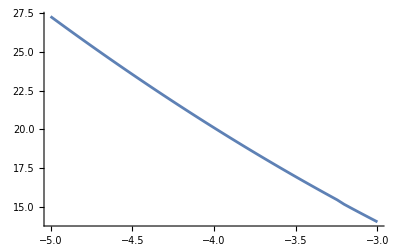

```mathematica
Plot[Fexp[Exp[z]],{z,-5,-3}]
```

```mathematica
dGcoeff={-1/5,-1/70,1/1050,299/323400,96917/525525000 , -107749/10032750000,-27333619/1876124250000, -308907281743/109790791110000000,1589498602063/4940585599950000000,28340195926465733/103406456606953500000000 };
```

```mathematica
Gsum[rho_,n_] := Sqrt[3](1+Sum[dGcoeff[[j]] Log[rho]^j,{j,1,n}])
```

```mathematica
GLtail[rho_] := Sqrt[Log[1/rho]]-rho^2 Sqrt[Log[1/rho]]+(1+Log[2Log[1/rho]])/2/Sqrt[Log[1/rho]]
```

```mathematica
GRtail[rho_] := Pi rho/(1+rho)^(3/2)+0.05
```

```mathematica
(* GLtail[rho_] := 0 *)
```

```mathematica
(* GRtail[rho_] := 0 *)
```

```mathematica
Gexp[rho_] := Gsum[rho,8]/;0.04<rho<32.88
```

```mathematica
Gexp[rho_] := GLtail[rho]/;rho<0.04
```

```mathematica
Gexp[rho_] := GRtail[rho]/;rho>32.88
```

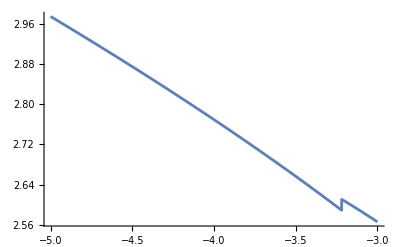

```mathematica
Plot[Gexp[Exp[z]],{z,-5,-3}]
```

```mathematica
thetahatexp[rho_,t_] := 1/(2Pi t)Gexp[rho] Exp[-1/t(-Pi^2/2+Fexp[rho])]
```

```mathematica
thetaHWexp[r_,t_] := thetahatexp[r t,t]
```

```mathematica
(* The density of 1/t A(t,mu) depends on H(rho,a)=F(rho)-pi^2/+ (1+a^2*rho^2)/(2a) *)
```

```mathematica
Hexp[rho_,a_] := Fexp[rho]-Pi^2/2 + (1+a^2 rho^2)/(2a)
```

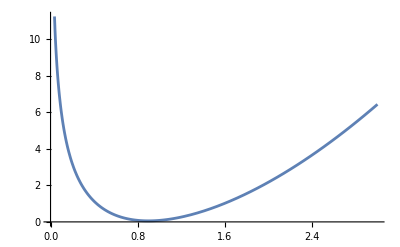

```mathematica
Plot[Hexp[rho,1.5],{rho,0,3}]
```

```mathematica
integrandAdensity[x_,a_,mu_,t_] := x^mu Gexp[x] Exp[-1/t Hexp[x,a]]/x
```

```mathematica
numAIntegral[a_,mu_,t_] := NIntegrate[integrandAdensity[x,a,mu,t], {x,0,Infinity}]
```

```mathematica
Adensity[a_,mu_,t_] := 1/(2Pi t) Exp[-1/2 mu^2 t] a^(mu-1) numAIntegral[a,mu,t]
```

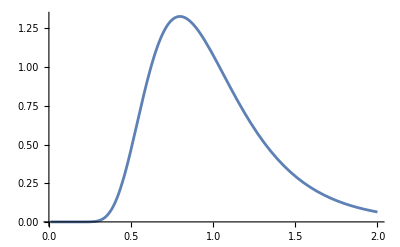

```mathematica
pA1=Plot[Adensity[a,-1,0.1],{a,0.01,2}]
```

```mathematica
(* Change of variable x = Exp[z] *)
```

```mathematica
intAdensityLog[z_,a_,mu_,t_] := Exp[mu z] Gexp[Exp[z]]Exp[-1/t Hexp[Exp[z],a]]
```

```mathematica
numAIntegralLog[a_,mu_,t_] := NIntegrate[intAdensityLog[z,a,mu,t], {z,-Infinity,Infinity}]
```

```mathematica
AdensityLog[a_,mu_,t_] := 1/(2Pi t) Exp[-1/2 mu^2 t] a^(mu-1) numAIntegralLog[a,mu,t]
```

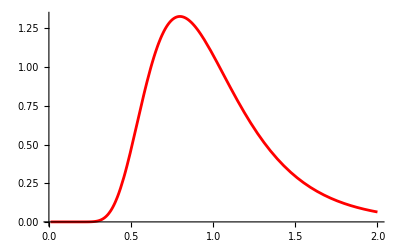

```mathematica
pA2=Plot[AdensityLog[a,-1,0.1],{a,0.01,2}, PlotStyle-> Red]
```

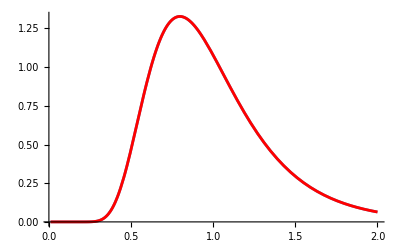

```mathematica
Show[pA1,pA2]
```

```mathematica
(* Normalization integral n(t) *)
```

```mathematica
normInt1DLog[mu_,t_] := 1/(Pi t) Exp[-1/2 mu^2 t] NIntegrate[Gexp[Exp[z]] BesselK[-mu,Exp[z]/t] Exp[-1/t(Fexp[Exp[z]]-Pi^2/2)],{z,-Infinity,Infinity}]
```

```mathematica
(* Two-dimensional integration for European option pricing *)
```

```mathematica
NCDF[x_] = 1/2(1+Erf[x/Sqrt[2]])
```

1/2 (1+Erf[x/(√2)])

```mathematica
d1[k_,f_,sig_]:=1/sig(Log[f/k]+1/2 sig^2)
```

```mathematica
d2[k_,f_,sig_]:=1/sig (Log[f/k]-1/2 sig^2)
```

```mathematica
CBS[k_,f_,sig_] := f NCDF[d1[k,f,sig]]-k NCDF[d2[k,f,sig]]
```

```mathematica
impvolC[k_,c_]:= v/.FindRoot[CBS[k,1,v]==c,{v,0.1}]
```

```mathematica
(* Denote tau=omega^2*T, nu=sigma0^2*T; mu=-1/2 *)
```

```mathematica
kernelC[k_,z_,a_,mu_,t_,sig0_] := (a Exp[z])^mu Gexp[Exp[z]] Exp[-1/t(Fexp[Exp[z]]-Pi^2/2)] CBS[k,1,sig0 Sqrt[t a]]Exp[-(1+a^2 Exp[2z])/(2a t)] 1/a
```

```mathematica
kernelClogA[k_,z_,a_,mu_,t_,sig0_] := (Exp[a+z])^mu Gexp[Exp[z]] Exp[-1/t(Fexp[Exp[z]]-Pi^2/2)] CBS[k,1,sig0 Sqrt[t] Exp[a/2]]Exp[-(1+Exp[2(z+a)])/(2Exp[a] t)]
```

```mathematica
cBSreduced[k_,mu_,t_,sig0_] := 1/(2Pi t) Exp[-1/2 mu^2 t] NIntegrate[kernelC[k,z,a,mu,t,sig0],{z,-Infinity,Infinity},{a,0,Infinity}, Method->{"NewtonCotesRule","Type"->"Closed"},  MaxRecursion -> 100]
```

```mathematica
cBSreduced2[k_,mu_,t_,sig0_] := 1/(2Pi t) Exp[-1/2 mu^2 t]NIntegrate[kernelC[k,z,a,mu,t,sig0],{z,-5,5},{a,0,10}, Method->"TrapezoidalRule"]
```

```mathematica
cBSreduced3[k_,mu_,t_,sig0_] := 1/(2Pi t) Exp[-1/2 mu^2 t]NIntegrate[kernelC[k,z,a,mu,t,sig0],{z,-5,5},{a,0,20}]
```

```mathematica
cBSreduced4[k_,mu_,t_,sig0_] := 1/(2Pi t) Exp[-1/2 mu^2 t]NIntegrate[kernelClogA[k,z,a,mu,t,sig0],{z,-10,10},{a,-10,10}]
```

```mathematica
Plot3D[kernelC[1,z,a,-0.5,1.0,0.2],{z,-5,5},{a,0,10},PlotRange -> {-0.1,1}]
```

General::munfl: 2.62514×10^-7 5.92041×10^-304 is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

```mathematica
(* f0[a,lam*a]. Denote tau=om^2*t and sig0r=sig0/om. Lam=Exp[z],a=Log[x] *)
```

```mathematica
IHW[a_,z_] := (1+(a Exp[z])^2)/(2a)+Fexp[Exp[z]]-Pi^2/2
```

```mathematica
f0HW[a_,z_,t_,mu_] := 1/(2Pi t) Exp[-1/2 mu^2 t] (a Exp[z])^mu Gexp[Exp[z]]Exp[-1/t IHW[a,z]]
```

```mathematica
f0HW[0.1,0,0.1,-1/2]
```

2.21833×10^-17

General::munfl: Exp[-122368.] is too small to represent as a normalized machine number; precision may be lost.

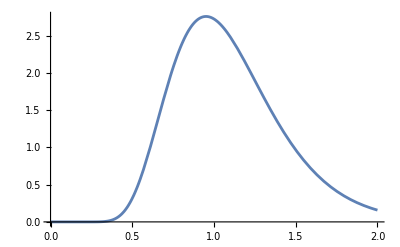

```mathematica
Plot[f0HW[a,0,0.1,-1/2],{a,0,2}]
```

```mathematica
sig0=0.2;om=1.0;
```

```mathematica
sig0r=sig0/om;
```

```mathematica
d1HW[a_,z_,tau_,k_,rho_] := 1/(Sqrt[1-rho^2] sig0r Sqrt[tau a])(-Log[k]+rho sig0r (a Exp[z]-1)-1/2 rho^2 sig0r^2 tau a+1/2 (1-rho^2)sig0r^2 tau a)
```

```mathematica
d2HW[a_,z_,tau_,k_,rho_] := 1/(Sqrt[1-rho^2] sig0r Sqrt[tau a])(-Log[k]+rho sig0r (a Exp[z]-1)-1/2 rho^2 sig0r^2 tau a-1/2 (1-rho^2)sig0r^2 tau a)
```

```mathematica
d1HW[a,z,tau,k,0]
```

(5. (0.+0.02 a tau-Log[k]))/(√(a tau))

```mathematica
cBSkernel[a_,z_,tau_,k_,rho_] := Exp[rho sig0r (a Exp[z]-1)-1/2 rho^2 sig0r^2 tau a]NCDF[d1HW[a,z,tau,k,rho]]-k NCDF[d2HW[a,z,tau,k,rho]]
```

```mathematica
cBSkernelLoga[x_,z_,tau_,k_,rho_] := Exp[rho sig0r (Exp[x+z]-1)-1/2 rho^2 sig0r^2 tau Exp[x]]NCDF[d1HW[Exp[x],z,tau,k,rho]]-k NCDF[d2HW[Exp[x],z,tau,k,rho]]
```

```mathematica
cBSkernel[1.0,0.0,0.1,1.0,0]
```

0.0252271

```mathematica
cBSHW[k_,tau_,rho_] := NIntegrate[1/a cBSkernel[a,z,tau,k,rho] f0HW[a,z,tau,-0.5],{z,-Infinity,Infinity},{a,0,Infinity}, Method->{"NewtonCotesRule","Type"->"Closed"},  MaxRecursion -> 100]
```

```mathematica
cBSHWLoga[k_,tau_,rho_] := NIntegrate[cBSkernelLoga[x,z,tau,k,rho] f0HW[Exp[x],z,tau,-0.5],{z,-Infinity,Infinity},{x,-Infinity,Infinity}, Method->{"NewtonCotesRule","Type"->"Closed"},  MaxRecursion -> 100]
```

```mathematica
cBSHW[1.0,1.0,0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.0865962

```mathematica
cBSHWLoga[1.0,1.0,0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.0865962

```mathematica
(* rho=0 *)
```

```mathematica
d1HWrho0[a_,tau_,k_] := 1/(sig0r Sqrt[tau a])(-Log[k]+1/2 sig0r^2 tau a)
```

```mathematica
d2HWrho0[a_,tau_,k_] := 1/(sig0r Sqrt[tau a])(-Log[k]-1/2 sig0r^2 tau a)
```

```mathematica
cBSkernelrho0[a_,tau_,k_] := NCDF[d1HWrho0[a,tau,k]]-k NCDF[d2HWrho0[a,tau,k]]
```

```mathematica
cBSHWrho0[k_,tau_] := NIntegrate[f0HW[a,z,tau,-0.5] cBSkernelrho0[a,tau,k],{z,-Infinity,Infinity},{a,0,Infinity}, Method->{"NewtonCotesRule","Type"->"Closed"},  MaxRecursion -> 100]
```

```mathematica
cBSHWrho0Loga[k_,tau_] := NIntegrate[f0HW[Exp[x],z,tau,-0.5] cBSkernelrho0[Exp[x],tau,k],{z,-Infinity,Infinity},{x,-Infinity,Infinity}, Method->{"NewtonCotesRule","Type"->"Closed"},  MaxRecursion -> 100]
```

```mathematica
cBSHWrho0[1.0,1.0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.354895

```mathematica
cBSHWrho0Loga[1.0,1.0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.0865962

```mathematica
normInt1DLog[-0.5,1.0]
```

1.01351

```mathematica
(* Uncorrelated case rho=0; ATM options *)
```

```mathematica
priceT025=1000 cBSHWrho0Loga[1.0,0.25]/normInt1DLog[-0.5,0.25]
```

40.6875

```mathematica
priceT1=1000 cBSHWrho0Loga[1.0,1.0]/normInt1DLog[-0.5,1.0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

85.4417

```mathematica
priceT2=1000 cBSHWrho0Loga[1.0,2.0]/normInt1DLog[-0.5,2.0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 8.27009 and 0.0000159206 for the integral and error estimates.

124.223

```mathematica
priceT5=1000 cBSHWrho0Loga[1.0,5.0]/normInt1DLog[-0.5,5.0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 30.7797 and 0.000262881 for the integral and error estimates.

180.502

```mathematica
(* Same using the correlated formulas with rho = 0.0 *)
```

```mathematica
priceT025gen=1000 cBSHWLoga[1.0,0.25,0]/normInt1DLog[-0.5,0.25]
```

40.6875

```mathematica
priceT1gen=1000 cBSHWLoga[1.0,1.0,0]/normInt1DLog[-0.5,1.0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

85.4417

```mathematica
matT=List[0.25,1.0,2.0,5.0,50.0]
```

{0.25,1.,2.,5.,50.}

```mathematica
Table[{matT[[i]],1000 cBSHWLoga[1.0,matT[[i]],0]/normInt1DLog[-0.5,matT[[i]]]},{i,1,4}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 8.27009 and 0.0000159206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 30.7797 and 0.000262881 for the integral and error estimates.

{{0.25,40.6875},{1.,85.4417},{2.,124.223},{5.,180.502}}

```mathematica
TableForm[%]
```

0.25 | 40.6875
1. | 85.4417
2. | 124.223
5. | 180.502

```mathematica
Table[{250+250i,Timing[1000 cBSHWLoga[0.25+0.25i,0.25,0]/normInt1DLog[-0.5,0.25]]},{i,1,7}]
```

{{500,{5.37394,500.001}},{750,{5.4312,250.406}},{1000,{5.50661,40.6875}},{1250,{4.97074,1.47154}},{1500,{3.8816,0.097588}},{1750,{3.5283,0.0131981}},{2000,{3.1865,0.00283026}}}

```mathematica
TableForm[%]
```

500 | 5.37394
500.001
750 | 5.4312
250.406
1000 | 5.50661
40.6875
1250 | 4.97074
1.47154
1500 | 3.8816
0.097588
1750 | 3.5283
0.0131981
2000 | 3.1865
0.00283026

```mathematica
Table[{250+250i,Timing[1000 cBSHWLoga[0.25+0.25i,1.0,0]/normInt1DLog[-0.5,1.0]]},{i,1,7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{500,{5.07482,502.515}},{750,{5.37341,264.854}},{1000,{5.654,85.4417}},{1250,{5.24882,26.4854}},{1500,{4.48439,12.3915}},{1750,{3.99982,7.38151}},{2000,{3.80524,5.03079}}}

```mathematica
TableForm[%1336]
```

500 | 5.07482
502.515
750 | 5.37341
264.854
1000 | 5.654
85.4417
1250 | 5.24882
26.4854
1500 | 4.48439
12.3915
1750 | 3.99982
7.38151
2000 | 3.80524
5.03079

```mathematica
Table[{250+250i,Timing[1000 cBSHWLoga[0.25+0.25i,2.0,0]/normInt1DLog[-0.5,2.0]]},{i,1,7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 8.27009 and 0.0000159206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 8.27009 and 0.0000159206 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{500,{5.13611,512.653}},{750,{5.39965,289.181}},{1000,{5.23139,124.223}},{1250,{5.09169,61.3774}},{1500,{4.50843,40.5475}},{1750,{4.2972,30.8633}},{2000,{4.01049,25.3067}}}

```mathematica
TableForm[%]
```

500 | 5.13611
512.653
750 | 5.39965
289.181
1000 | 5.23139
124.223
1250 | 5.09169
61.3774
1500 | 4.50843
40.5475
1750 | 4.2972
30.8633
2000 | 4.01049
25.3067

```mathematica
Table[{250+250i,Timing[1000 cBSHWLoga[0.25+0.25i,5.0,0]/normInt1DLog[-0.5,5.0]]},{i,1,7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 30.7797 and 0.000262881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 30.7797 and 0.000262881 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{500,{6.09878,536.407}},{750,{6.27632,330.927}},{1000,{5.92396,180.502}},{1250,{5.3351,118.151}},{1500,{5.07111,93.8288}},{1750,{4.74343,80.9547}},{2000,{4.50553,72.8193}}}

```mathematica
TableForm[%]
```

500 | 6.09878
536.407
750 | 6.27632
330.927
1000 | 5.92396
180.502
1250 | 5.3351
118.151
1500 | 5.07111
93.8288
1750 | 4.74343
80.9547
2000 | 4.50553
72.8193

```mathematica
(* Correlated case rho=-0.75 *)
```

```mathematica
Table[{250+250i,Timing[1000 cBSHWLoga[0.25+0.25i,0.25,-0.75]/normInt1DLog[-0.5,0.25]]},{i,1,7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{500,{5.77146,500.027}},{750,{5.96686,251.426}},{1000,{5.70135,39.6175}},{1250,{5.01755,0.0332683}},{1500,{3.18569,0.000018003}},{1750,{2.95841,1.45074×10^-7}},{2000,{4.53381,4.81001×10^-9}}}

```mathematica
TableForm[%]
```

500 | 5.77146
500.027
750 | 5.96686
251.426
1000 | 5.70135
39.6175
1250 | 5.01755
0.0332683
1500 | 3.18569
0.000018003
1750 | 2.95841
1.45074×10^-7
2000 | 4.53381
4.81001×10^-9

```mathematica
Table[{250+250i,Timing[1000 cBSHWLoga[0.25+0.25i,1.0,-0.75]/normInt1DLog[-0.5,1.0]]},{i,1,7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{500,{5.54136,505.112}},{750,{5.56447,270.715}},{1000,{5.61154,77.0641}},{1250,{4.51256,4.87658}},{1500,{3.97226,0.490915}},{1750,{3.40544,0.115453}},{2000,{3.13802,0.0409306}}}

```mathematica
TableForm[%]
```

500 | 5.54136
505.112
750 | 5.56447
270.715
1000 | 5.61154
77.0641
1250 | 4.51256
4.87658
1500 | 3.97226
0.490915
1750 | 3.40544
0.115453
2000 | 3.13802
0.0409306

```mathematica
Table[{250+250i,Timing[1000 cBSHWLoga[0.25+0.25i,2.0,-0.75]/normInt1DLog[-0.5,2.0]]},{i,1,7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 8.27009 and 0.0000159206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 8.27009 and 0.0000159206 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{500,{5.01328,516.178}},{750,{5.32909,291.981}},{1000,{5.46648,103.323}},{1250,{4.5422,15.5282}},{1500,{4.22821,3.66236}},{1750,{3.83482,1.45961}},{2000,{3.49154,0.746325}}}

```mathematica
TableForm[%]
```

500 | 5.01328
516.178
750 | 5.32909
291.981
1000 | 5.46648
103.323
1250 | 4.5422
15.5282
1500 | 4.22821
3.66236
1750 | 3.83482
1.45961
2000 | 3.49154
0.746325

```mathematica
Table[{250+250i,Timing[1000 cBSHWLoga[0.25+0.25i,5.0,-0.75]/normInt1DLog[-0.5,5.0]]},{i,1,7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 30.7797 and 0.000262881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 30.7797 and 0.000262881 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{500,{5.66632,535.012}},{750,{5.62384,320.845}},{1000,{5.71424,135.668}},{1250,{4.7742,34.8173}},{1500,{4.64499,13.0739}},{1750,{4.21792,6.92228}},{2000,{3.97354,4.3134}}}

```mathematica
TableForm[%]
```

500 | 5.66632
535.012
750 | 5.62384
320.845
1000 | 5.71424
135.668
1250 | 4.7742
34.8173
1500 | 4.64499
13.0739
1750 | 4.21792
6.92228
2000 | 3.97354
4.3134

```mathematica
(* utilities *)
```

```mathematica
NCDF[x_] := 1/2(1+Erf[x/Sqrt[2]])
```

```mathematica
callBS[k_,v_]:= NCDF[-k/v+v/2]-Exp[k]NCDF[-k/v-v/2]
```

```mathematica
impvolCall[k_,c_]:= v/.FindRoot[callBS[k,v]==c,{v,0.1}]
```

```mathematica
cBSHWLoga[1.0,1.0,0.0]/normT1
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.0854417

```mathematica
impvolCall[0,0.0854417]
```

0.214582

```mathematica
(* Plot the implied vol rho=0 impvolC[k_,c_] *)
```

```mathematica
(2000-250)/100.0
```

17.5

```mathematica
CBS[k,f,t]
```

1/2 f (1+Erf[d1[k,f,t]/(√2)])-1/2 k (1+Erf[d2[k,f,t]/(√2)])

```mathematica
normT1=normInt1DLog[-0.5,5.0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.197}. NIntegrate obtained 30.7797 and 0.000262881 for the integral and error estimates.

1.04884

```mathematica
impvolsT5neg=Table[{Log[0.25+0.100i],1/Sqrt[5]impvolCall[Log[0.25+0.100i],cBSHWLoga[0.25+0.1i,5.0,-0.75]/normT1]},{i,1,18}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{-1.04982,0.360306},{-0.798508,0.316948},{-0.597837,0.279986},{-0.430783,0.247225},{-0.287682,0.217417},{-0.162519,0.189873},{-0.0512933,0.164475},{0.0487902,0.142263},{0.139762,0.126731},{0.223144,0.121287},{0.300105,0.122881},{0.371564,0.127307},{0.438255,0.132644},{0.500775,0.138165},{0.559616,0.143587},{0.615186,0.148803},{0.667829,0.153775},{0.71784,0.158499}}

```mathematica
impvolsT025={{-1.0498221244986778,0.4457107154216745},{-0.7985076962177716,0.38279284980815403},{-0.5978370007556204,0.3311960155789002},{-0.4307829160924542,0.2875786776969127},{-0.2876820724517809,0.2509342180833449},{-0.1625189294977748,0.22244090279398446},{-0.05129329438755046,0.20615267553569797},{0.04879016416943205,0.2059570550542432},{0.13976194237515863,0.21812132364909226},{0.22314355131420976,0.2354853155075888},{0.30010459245033816,0.25402220329877157},{0.3715635564324832,0.27220382607309984},{0.4382549309311553,0.2895279391095597},{0.5007752879124894,0.30586922543371975},{0.5596157879354227,0.3212401467741038},{0.6151856390902335,0.33570162180469987},{0.6678293725756556,0.3493283752853668},{0.7178397931503168,0.3621952880011191}};
```

```mathematica
impvolsT1={{-1.0498221244986778,0.44340684768797856},{-0.7985076962177716,0.38369766471754696},{-0.5978370007556204,0.3345086071657028},{-0.4307829160924542,0.2929906048669593},{-0.2876820724517809,0.25829165925872805},{-0.1625189294977748,0.23157463424155278},{-0.05129329438755046,0.21649802455048506},{0.04879016416943205,0.2163182269714153},{0.13976194237515863,0.22755833446561904},{0.22314355131420976,0.2437643747186824},{0.30010459245033816,0.26120466142585097},{0.3715635564324832,0.27840170526067665},{0.4382549309311553,0.29484294179836446},{0.5007752879124894,0.31038443777581953},{0.5596157879354227,0.325022544704898},{0.6151856390902335,0.3388057662840495},{0.6678293725756556,0.35179945828361264},{0.7178397931503168,0.36407138502428715}};
```

```mathematica
impvolsT2={{-1.0498221244986778,0.42800760997073484},{-0.7985076962177716,0.37400251303522886},{-0.5978370007556204,0.3293722850721718},{-0.4307829160924542,0.2916762205327645},{-0.2876820724517809,0.26025095333729326},{-0.1625189294977748,0.2362140132846016},{-0.05129329438755046,0.22277576545655944},{0.04879016416943205,0.2226164050311569},{0.13976194237515863,0.23262272259841948},{0.22314355131420976,0.24715482546828826},{0.30010459245033816,0.2628834609885175},{0.3715635564324832,0.27844802702899224},{0.4382549309311553,0.2933582761990202},{0.5007752879124894,0.3074666515989994},{0.5596157879354227,0.32075990468775933},{0.6151856390902335,0.3332765526059496},{0.6678293725756556,0.3450730178441105},{0.7178397931503168,0.35620940931849077}};
```

```mathematica
impvolsT5={{-1.0498221244986778,0.36044991030783147},{-0.7985076962177716,0.3195093521206266},{-0.5978370007556204,0.28561226239506177},{-0.4307829160924542,0.25700939401812517},{-0.2876820724517809,0.2332764181762058},{-0.1625189294977748,0.2152888098357427},{-0.05129329438755046,0.20534763241061618},{0.04879016416943205,0.20523069817187026},{0.13976194237515863,0.21262255757218274},{0.22314355131420976,0.2234517108432736},{0.30010459245033816,0.23525916779252026},{0.3715635564324832,0.24700193866783485},{0.4382549309311553,0.2582865293853556},{0.5007752879124894,0.26898461250151007},{0.5596157879354227,0.279075625356943},{0.6151856390902335,0.28858240486053355},{0.6678293725756556,0.2975439791873293},{0.7178397931503168,0.30600377081317515}};
```

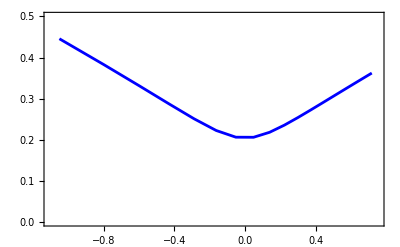

```mathematica
pNum025=ListPlot[impvolsT025,Joined -> True, PlotStyle-> Blue, Frame -> True,PlotRange -> {{-1.1,0.75},{0.0,0.5}}]
```

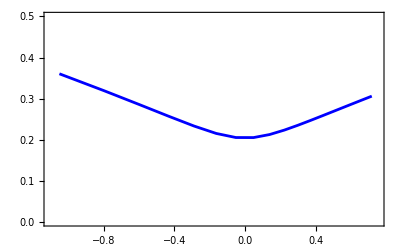

```mathematica
pNum5=ListPlot[impvolsT5,Joined -> True, PlotStyle-> Blue, Frame -> True,PlotRange -> {{-1.1,0.75},{0.0,0.5}}]
```

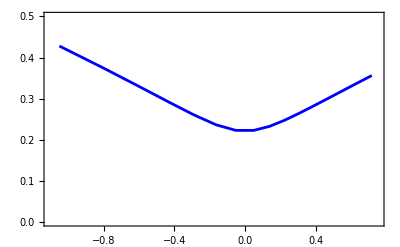

```mathematica
pNum2=ListPlot[impvolsT2,Joined -> True, PlotStyle-> Blue, Frame -> True,PlotRange -> {{-1.1,0.75},{0,0.5}}]
```

```mathematica
impvolCall[Log[0.5],0.502517]
```

0.358059

```mathematica
ivExactRho0T1={{0.5,0.358},{0.75,0.258},{1.0,0.2146},{1.25,0.2438},{1.5,0.28676},{1.75,0.325},{2.0,0.358}};
```

```mathematica
ivLogExactRho0T1={{Log[0.5],0.358},{Log[0.75],0.258},{Log[1.0],0.2146},{Log[1.25],0.2438},{Log[1.5],0.28676},{Log[1.75],0.325},{Log[2.0],0.358}};
```

```mathematica
ivExactRho0T025={{0.5,0.356},{0.75,0.251},{1.0,0.204},{1.25,0.235},{1.5,0.281},{1.75,0.321},{2.0,0.356}};
```

```mathematica
ivExactRho0T2={{0.5,0.351},{0.75,0.260},{1.0,0.221},{1.25,0.247},{1.5,0.286},{1.75,0.321},{2.0,0.351}};
```

```mathematica
ivLogExactRho0T2={{Log[0.5],0.351},{Log[0.75],0.260},{Log[1.0],0.221},{Log[1.25],0.247},{Log[1.5],0.286},{Log[1.75],0.321},{Log[2.0],0.351}};
```

```mathematica
ivExactRho0T5={{0.5,0.302},{0.75,0.234},{1.0,0.205},{1.25,0.224},{1.5,0.253},{1.75,0.280},{2.0,0.302}};
```

```mathematica
ivLogExactRho0T5={{Log[0.5],0.302},{Log[0.75],0.234},{Log[1.0],0.205},{Log[1.25],0.224},{Log[1.5],0.253},{Log[1.75],0.280},{Log[2.0],0.302}};
```

```mathematica
ivLogExactRho0T025={{Log[0.5],0.356},{Log[0.75],0.251},{Log[1.0],0.204},{Log[1.25],0.235},{Log[1.5],0.281},{Log[1.75],0.321},{Log[2.0],0.356}};
```

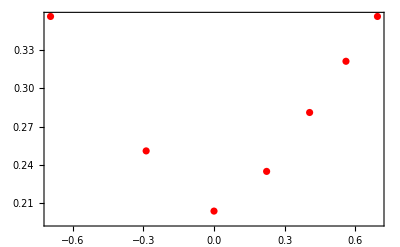

```mathematica
pEx025=ListPlot[ivLogExactRho0T025,Joined -> False, PlotStyle-> Red, Frame -> True]
```

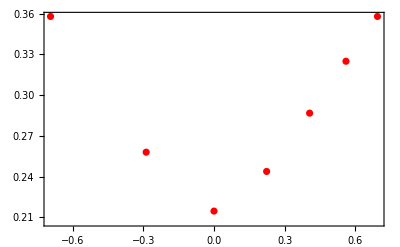

```mathematica
pEx1=ListPlot[ivLogExactRho0T1,Joined -> False, PlotStyle-> Red, Frame -> True]
```

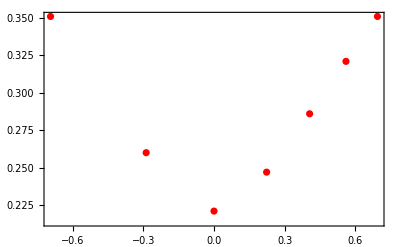

```mathematica
pEx2=ListPlot[ivLogExactRho0T2,Joined -> False, PlotStyle-> Red, Frame -> True]
```

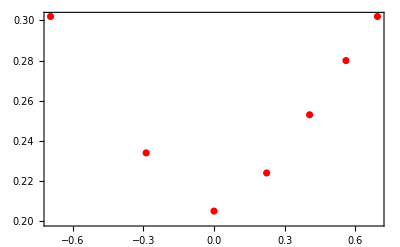

```mathematica
pEx5=ListPlot[ivLogExactRho0T5,Joined -> False, PlotStyle-> Red, Frame -> True]
```

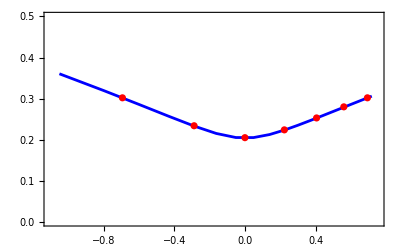

```mathematica
Show[pNum5,pEx5]
```

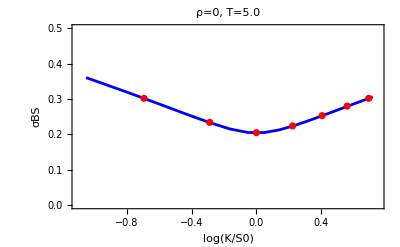

```mathematica
Show[%1537,FrameLabel->{{HoldForm[σBS],None},{HoldForm[Log[K/S0]],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{"ρ","=","0"}],","," ",RowBox[{"T","=","5.0"}]}]],LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRLogRho0T5.eps",%1538,"EPS"]
```

/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRLogRho0T5.eps

```mathematica
(* Negative correlation rho=-0.75 *)
```

```mathematica
normT1=normInt1DLog[-0.5,0.25]
```

1.00352

```mathematica
impvolsT025neg=Table[{Log[0.25+0.100i],1/Sqrt[0.25]impvolCall[Log[0.25+0.100i],cBSHWLoga[0.25+0.1i,0.25,-0.75]/normT1]},{i,1,18}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{-1.04982,0.533641},{-0.798508,0.462375},{-0.597837,0.40239},{-0.430783,0.349731},{-0.287682,0.302117},{-0.162519,0.258203},{-0.0512933,0.217522},{0.0487902,0.181504},{0.139762,0.156414},{0.223144,0.14936},{0.300105,0.15463},{0.371564,0.164368},{0.438255,0.175305},{0.500775,0.186318},{0.559616,0.197012},{0.615186,0.207252},{0.667829,0.217005},{0.71784,0.226279}}

```mathematica
ivLogExactRhom075T025={{Log[0.5],0.431},{Log[0.75],0.302},{Log[1.0],0.1987},{Log[1.25],0.14936},{Log[1.5],0.16987},{Log[1.75],0.19707},{Log[2.0],0.2217}};
```

```mathematica
ivLogExactRhom075T1={{Log[0.5],0.40655},{Log[0.75],0.28815},{Log[1.0],0.19349},{Log[1.25],0.14886},{Log[1.5],0.16627},{Log[1.75],0.18997},{Log[2.0],0.2114}};
```

```mathematica
ivLogExactRhom075T2={{Log[0.5],0.37372},{Log[0.75],0.26822},{Log[1.0],0.18373},{Log[1.25],0.14358},{Log[1.5],0.15746},{Log[1.75],0.17725},{Log[2.0],0.19523}};
```

```mathematica
ivLogExactRhom075T5={{Log[0.5],0.298},{Log[0.75],0.2177},{Log[1.0],0.153},{Log[1.25],0.121},{Log[1.5],0.130},{Log[1.75],0.1438},{Log[2.0],0.156}};
```

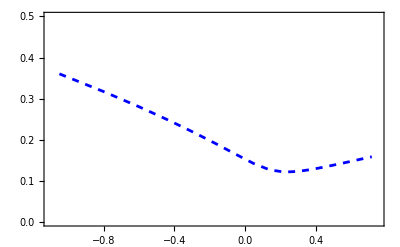

```mathematica
pNum5neg=ListPlot[impvolsT5neg,Joined -> True, PlotStyle->{Blue,Dashed}, Frame -> True,PlotRange -> {{-1.1,0.75},{0.0,0.5}}]
```

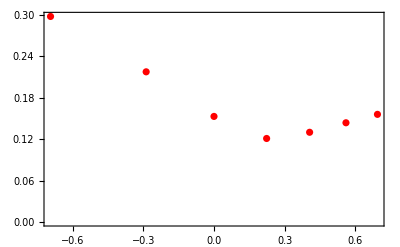

```mathematica
pEx5m=ListPlot[ivLogExactRhom075T5,Joined -> False, PlotStyle-> Red, Frame -> True]
```

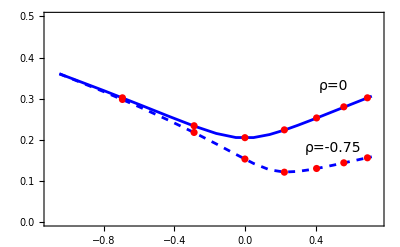

```mathematica
Show[pNum5neg,pEx5m,pNum5,pEx5,Epilog-> {Text[Style["ρ=0",FontSize-> 14], {0.5,0.33}],Text[Style["ρ=-0.75",FontSize-> 14], {0.5,0.18}]}]
```

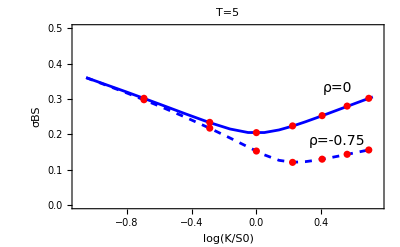

```mathematica
Show[%1558,FrameLabel->{{HoldForm[σBS],None},{HoldForm[Log[K/S0]],None}},PlotLabel->HoldForm[T=5],LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRT5combined.eps",%1559,"EPS"]
```

/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRT5combined.eps

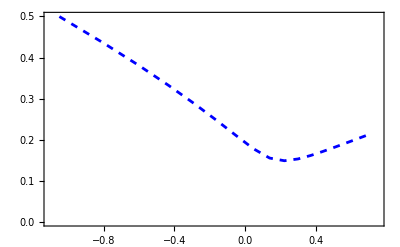

```mathematica
pNum1neg=ListPlot[impvolsT1neg,Joined -> True, PlotStyle->{Blue,Dashed}, Frame -> True,PlotRange -> {{-1.1,0.75},{0.0,0.5}}]
```

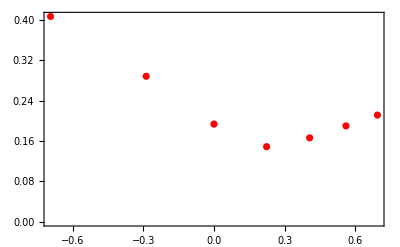

```mathematica
pEx1m=ListPlot[ivLogExactRhom075T1,Joined -> False, PlotStyle-> Red, Frame -> True]
```

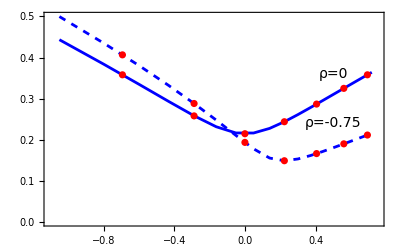

```mathematica
Show[pNum1neg,pEx1m,pNum1,pEx1,Epilog-> {Text[Style["ρ=0",FontSize-> 14], {0.5,0.36}],Text[Style["ρ=-0.75",FontSize-> 14], {0.5,0.24}]}]
```

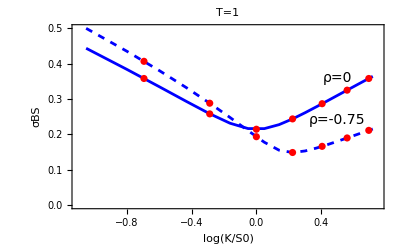

```mathematica
Show[%1569,FrameLabel->{{HoldForm[σBS],None},{HoldForm[Log[K/S0]],None}},PlotLabel->HoldForm[T=1],LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRT1combined.eps",%1570,"EPS"]
```

/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRT1combined.eps

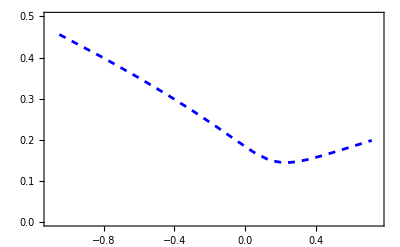

```mathematica
pNum2neg=ListPlot[impvolsT2neg,Joined -> True, PlotStyle->{Blue,Dashed}, Frame -> True,PlotRange -> {{-1.1,0.75},{0.0,0.5}}]
```

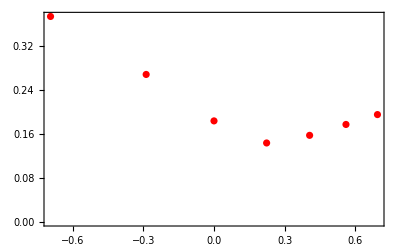

```mathematica
pEx2m=ListPlot[ivLogExactRhom075T2,Joined -> False, PlotStyle-> Red, Frame -> True]
```

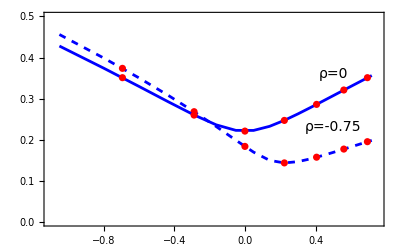

```mathematica
Show[pNum2neg,pEx2m,pNum2,pEx2,Epilog-> {Text[Style["ρ=0",FontSize-> 14], {0.5,0.36}],Text[Style["ρ=-0.75",FontSize-> 14], {0.5,0.23}]}]
```

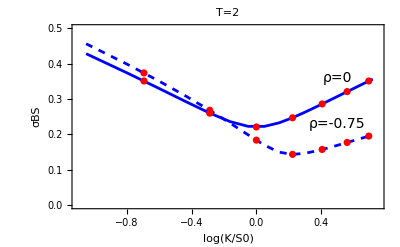

```mathematica
Show[%1578,FrameLabel->{{HoldForm[σBS],None},{HoldForm[Log[K/S0]],None}},PlotLabel->HoldForm[T=2],LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRT2combined.eps",%1579,"EPS"]
```

/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRT2combined.eps

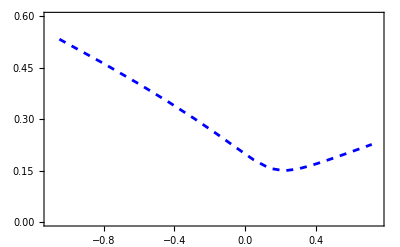

```mathematica
pNum025neg=ListPlot[impvolsT025neg,Joined -> True, PlotStyle->{Blue,Dashed}, Frame -> True,PlotRange -> {{-1.1,0.75},{0.0,0.6}}]
```

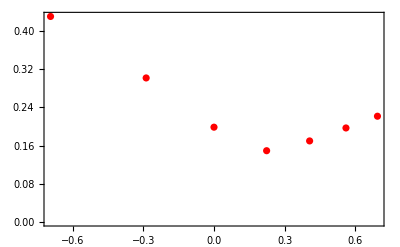

```mathematica
pEx025m=ListPlot[ivLogExactRhom075T025,Joined -> False, PlotStyle-> Red, Frame -> True]
```

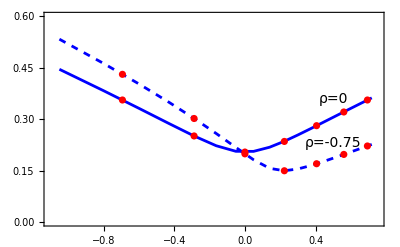

```mathematica
Show[pNum025neg,pEx025m,pNum025,pEx025,Epilog-> {Text[Style["ρ=0",FontSize-> 14], {0.5,0.36}],Text[Style["ρ=-0.75",FontSize-> 14], {0.5,0.23}]}]
```

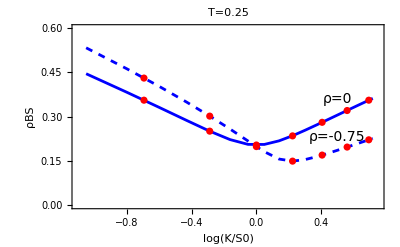

```mathematica
Show[%1590,FrameLabel->{{HoldForm[ρBS],None},{HoldForm[Log[K/S0]],None}},PlotLabel->HoldForm[T=0.25],LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Export["/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRT025combined.eps",%1591,"EPS"]
```

/Users/dpirjol/projects/papers/HartmanWatson/conditional distribution/plots/SABRT025combined.eps

```mathematica
(* Plot the integrand *)
```

```mathematica
Plot3D[f0HW[a,z,1.0,-0.5] cBSkernelrho0[a,1.0,1],{a,0,5},{z,-2,2}]
```

-Graphics3D-